```mathematica
Clear[S,Sp,EE,II,R,Iall,Ep,Ip,Rp,dv,db,t,qem,p,q];
```

```mathematica
c[+1]=0.2;
c[00]=0.5;
c[-1]=0.3;
```

```mathematica
ρ[-1,-1]=0.001;(* The ρ might be made up*)
ρ[+1,-1]=0.01;
ρ[+1,+1]=0.002;
```

```mathematica
γ[-1,-1,p,+1]=γ[+1,+1,p,+1]= 3.0 10^-3;
γ[-1,-1,p,00]=γ[+1,+1,p,00]=2.0 10^-3;
γ[-1,-1,p,-1]=γ[+1,+1,p,-1]= 9.13 10^-4;

α=0.5; (* This fixes issues with β/γ variations as population sizes vary *)

γ[+1,+1,p,+1]=α γ[+1,+1,p,+1];
γ[+1,+1,p,00]=α γ[+1,+1,p,00];
γ[+1,+1,p,-1]=α γ[+1,+1,p,-1];


γ[-1,-1,q,+1]=γ[+1,+1,q,+1]=γ[-1,-1,p,+1];
γ[-1,-1,q,00]=γ[+1,+1,q,00]=γ[-1,-1,p,00];
γ[-1,-1,q,-1]=γ[+1,+1,q,-1]=γ[-1,-1,p,-1];

γ[+1,-1,p,+1]=2.0 10^-3;
γ[+1,-1,p,00]=1.5 10^-3;
γ[+1,-1,p,-1]=3.0 10^-4;

γ[+1,-1,q,+1]=γ[+1,-1,p,+1];
γ[+1,-1,q,00]=γ[+1,-1,p,00];
γ[+1,-1,q,-1]=γ[+1,-1,p,-1];
```

```mathematica
ϕ[-1,-1,+1]=0.011515597;
ϕ[-1,-1,00]=0.024290712;
ϕ[-1,-1,-1]=0.002272815;

ϕ[+1,-1,+1]=0.023750918;
ϕ[+1,-1,00]=0.042417655;
ϕ[+1,-1,-1]=0.010312899;

ϕ[+1,+1,+1]=0.011515597;
ϕ[+1,+1,00]=0.024290712;
ϕ[+1,+1,-1]=0.002272815;

θ[-1,00]=1.05 10^-2;
θ[00,-1]=1.05 10^-2;
```

```mathematica
β0=1/10 1/365 8.5 10^-6 1/10^6; (* this β0 comes from a q strain, the 1/10 is a tweak... ?*)

β[-1,-1,q][cf_]=β0 n ic;
β[-1,-1,p][cf_]=1/cf γ[-1,-1,q,+1]/γ[-1,-1,q,-1] β[-1,-1,q][cf];

β[+1,-1,q][cf_]=1.1β0 n (1-ic)aa;
β[+1,-1,p][cf_]= 1/cf γ[+1,-1,q,+1]/γ[+1,-1,q,-1] β[+1,-1,q][cf];

β[+1,+1,q][cf_]=β0 n (1-ic)hh; 
β[+1,+1,p][cf_]=1/cf γ[+1,+1,q,+1]/γ[+1,+1,q,-1] β[+1,+1,q][cf];
```

```mathematica
ζ0=1/365 0.88; (* Also from q-strain measurements, updated *)

ζ[-1,-1,q]=ζ0; 
ζ[-1,-1,p]=ζ0;

ζ[+1,-1,q]=1.1ζ0;
ζ[+1,-1,p]=1.1ζ0;

ζ[+1,+1,q]=ζ0 ;
ζ[+1,+1,p]=ζ0;
```

```mathematica
ω=4.45 10^-5;
ωb=8.22 10^-4;
ωbv=3.3 ωb;
ωv=2 10^-3;

α=6.9 10^-5;
```

```mathematica
MyEqS[i_,j_][cf_]:=-(β[i,j,p] [cf]Iall[p][t] +β[i,j,q] [cf]Iall[q][t])S[i,j][t]+
ρ[i,j] R[i,j][t]-ω S[i,j][t];
MyEqE[i_,j_,k_][cf_]:=β[i,j,k][cf] S[i,j][t]Iall[k][t]-ζ[i,j,k] EE[i,j,k][t]-ω EE[i,j,k][t];
MyEqI[i_,j_,k_,l_,noq_]:=ζ[i,j,k] c[l] EE[i,j,k][t]-γ[i,j,k,l] II[i,j,k,l][t]+If[SameQ[k,p],-1,+1]If[noq,0,ϕ[i,j,l] ]II[i,j,p,l][t]+Which[l==+1,0,l==0,-1,l==-1,+1](θ[00,-1] II[i,j,k,00][t]-θ[-1,00] II[i,j,k,-1][t])+-ω II[i,j,k,l][t];
MyEqR[i_,j_]:=∑_(l=-1)^1 (γ[i,j,p,l]II[i,j,p,l][t]+γ[i,j,q,l]II[i,j,q,l][t])-ρ[i,j]R[i,j][t]-ω R[i,j][t];
EQN[cf_,noq_]:={

S[-1,-1]'[t]==MyEqS[-1,-1][cf]+
α (S[-1,-1][t]+S[+1,+1][t]+Sp[+1,+1][t]+
EE[-1,-1,p][t]+EE[-1,-1,q][t]+EE[+1,+1,p][t]+EE[+1,+1,q][t]+Ep[+1,+1][t]+
II[-1,-1,p,+1][t]+II[+1,+1,p,+1][t]+
R[-1,-1][t]+R[+1,+1][t]+Rp[+1,+1][t]),

S[+1,-1]'[t]==MyEqS[+1,-1][cf]+
α(S[+1,-1][t]+EE[+1,-1,p][t]+ EE[+1,-1,q][t]+R[+1,-1][t])-
ωv S[+1,-1][t],

S[+1,+1]'[t]==MyEqS[+1,+1][cf],

Sp[+1,-1]'[t]==-β[+1,-1,q][cf]Sp[+1,-1][t]Iall[q][t]+ρ[+1,-1]Rp[+1,-1][t]-ω Sp[+1,-1][t]-ωv Sp[+1,-1][t],

Sp[+1,+1]'[t]==-β[+1,+1,q][cf]Sp[+1,+1][t]Iall[q][t]+ρ[+1,+1]Rp[+1,-1][t]-ω Sp[+1,+1][t]
+α(Sp[+1,-1][t]+Ep[+1,-1][t]+Rp[+1,-1][t]),

EE[-1,-1,p]'[t]==MyEqE[-1,-1,p][cf],
EE[-1,-1,q]'[t]==If[noq,0,MyEqE[-1,-1,q][cf]],

EE[+1,-1,p]'[t]==MyEqE[+1,-1,p][cf]-ωv EE[+1,-1,p][t],
EE[+1,-1,q]'[t]==If[noq,0,MyEqE[+1,-1,q][cf]-ωv EE[+1,-1,q][t]],

EE[+1,+1,p]'[t]==MyEqE[+1,+1,p][cf],
EE[+1,+1,q]'[t]==MyEqE[+1,+1,q][cf],

Ep[+1,-1]'[t]==β[+1,-1,q][cf]Sp[+1,-1][t]Iall[q][t]-ζ[+1,-1,q]c[+1]Ep[+1,-1][t]-ωv Ep[+1,-1][t],
Ep[+1,+1]'[t]==β[+1,+1,q][cf]Sp[+1,+1][t]Iall[q][t]-ζ[+1,+1,q]c[+1]Ep[+1,+1][t],

Eall[t]==EE[-1,-1,p][t]+EE[-1,-1,q][t]+EE[+1,-1,p][t]+EE[+1,-1,q][t]+EE[+1,+1,p][t]+EE[+1,+1,q][t]+Ep[+1,-1][t]+Ep[+1,+1][t],

dEp[t]==β[-1,-1,p][cf] S[-1,-1][t]Iall[p][t]+β[+1,-1,p][cf] S[+1,-1][t]Iall[p][t]+β[+1,+1,p][cf] S[+1,+1][t]Iall[p][t],

II[-1,-1,p,+1]'[t]==MyEqI[-1,-1,p,+1,noq],
II[-1,-1,p,00]'[t]==MyEqI[-1,-1,p,00,noq]+α(II[-1,-1,p,00][t]+II[+1,+1,p,00][t])-
ωb II[-1,-1,p,00][t],
II[-1,-1,p,-1]'[t]==MyEqI[-1,-1,p,-1,noq]+α(II[-1,-1,p,-1][t]+II[+1,+1,p,-1][t])-
ωb II[-1,-1,p,-1][t],
II[-1,-1,q,+1]'[t]==MyEqI[-1,-1,q,+1,noq]+α(II[-1,-1,q,+1][t]+II[+1,+1,q,+1][t])
-ωb II[-1,-1,q,+1][t],
II[-1,-1,q,00]'[t]==MyEqI[-1,-1,q,00,noq]+α(II[-1,-1,q,00][t]+II[+1,+1,q,00][t])-
ωb II[-1,-1,q,00][t],
II[-1,-1,q,-1]'[t]==MyEqI[-1,-1,q,-1,noq]+
α(II[-1,-1,q,-1][t]+II[+1,+1,q,-1][t]+Ip[+1,+1,q,+1][t])-
ωb II[-1,-1,q,-1][t],

II[+1,-1,p,+1]'[t]==MyEqI[+1,-1,p,+1,noq]-ωv II[+1,-1,p,+1][t],
II[+1,-1,p,00]'[t]==MyEqI[+1,-1,p,00,noq]+α II[+1,-1,p,00][t]-(ωbv+ωv)II[+1,-1,p,00][t],
II[+1,-1,p,-1]'[t]==MyEqI[+1,-1,p,-1,noq]+α II[+1,-1,p,-1][t]-(ωbv+ωv)II[+1,-1,p,-1][t],
II[+1,-1,q,+1]'[t]==MyEqI[+1,-1,q,+1,noq]+α II[+1,-1,q,+1][t]-(ωbv+ωv)II[+1,-1,q,+1][t],
II[+1,-1,q,00]'[t]==MyEqI[+1,-1,q,00,noq]+α II[+1,-1,q,00][t]-(ωbv+ωv)II[+1,-1,q,00][t],
II[+1,-1,q,-1]'[t]==MyEqI[+1,-1,q,-1,noq]+α II[+1,-1,q,-1][t]-(ωbv+ωv)II[+1,-1,q,-1][t],

II[+1,+1,p,+1]'[t]==MyEqI[+1,+1,p,+1,noq],
II[+1,+1,p,00]'[t]==MyEqI[+1,+1,p,00,noq]-ωb II[+1,+1,p,00][t],
II[+1,+1,p,-1]'[t]==MyEqI[+1,+1,p,-1,noq]-ωb II[+1,+1,p,-1][t],
II[+1,+1,q,+1]'[t]==MyEqI[+1,+1,q,+1,noq]-ωb II[+1,+1,q,+1][t],
II[+1,+1,q,00]'[t]==MyEqI[+1,+1,q,00,noq]-ωb II[+1,+1,q,00][t],
II[+1,+1,q,-1]'[t]==MyEqI[+1,+1,q,-1,noq]-ωb II[+1,+1,q,-1][t],

Ip[+1,-1,q,+1]'[t]==ζ[+1,-1,q]c[+1]Ep[+1,-1][t]-γ[+1,-1,q,+1]Ip[+1,-1,q,+1][t]
+α Ip[+1,-1,q,+1][t]-(ωbv+ωb)Ip[+1,-1,q,+1][t],

Ip[+1,+1,q,+1]'[t]==ζ[+1,+1,q]c[+1]Ep[+1,+1][t]-γ[+1,+1,q,+1]Ip[+1,+1,q,+1][t]-
ωb Ip[+1,+1,q,+1][t],

Iall[p][t]==
II[-1,-1,p,+1][t]+II[-1,-1,p,00][t]+II[-1,-1,p,-1][t]+
II[+1,-1,p,+1][t]+II[+1,-1,p,00][t]+II[+1,-1,p,-1][t]+
II[+1,+1,p,+1][t]+II[+1,+1,p,00][t]+II[+1,+1,p,-1][t],

Iall[q][t]==
II[-1,-1,q,+1][t]+II[-1,-1,q,00][t]+II[-1,-1,q,-1][t]+
II[+1,-1,q,+1][t]+II[+1,-1,q,00][t]+II[+1,-1,q,-1][t]+
II[+1,+1,q,+1][t]+II[+1,+1,q,00][t]+II[+1,+1,q,-1][t]+Ip[+1,+1,q,+1][t]+Ip[+1,-1,q,+1][t],

R[-1,-1]'[t]==MyEqR[-1,-1],

R[+1,-1]'[t]==MyEqR[+1,-1]-ωv R[+1,-1][t],

R[+1,+1]'[t]==MyEqR[+1,+1],

Rp[+1,-1]'[t]==γ[+1,-1,q,+1]Ip[+1,-1,q,+1][t]-ρ[+1,-1]Rp[+1,-1][t]-ωv Rp[+1,-1][t],
Rp[+1,+1]'[t]==γ[+1,+1,q,+1]Ip[+1,+1,q,+1][t]-ρ[+1,+1]Rp[+1,+1][t],

trans1'[t]==β[-1,-1,p][cf]S[-1,-1][t](II[-1,-1,p,+1][t]+II[-1,-1,p,00][t]+II[-1,-1,p,-1][t]), (* IC to IC *)

trans2'[t]==(β[+1,-1,p][cf]S[+1,-1][t]+β[+1,+1,p][cf]S[+1,+1][t]+β[+1,-1,p][cf]Sp[+1,-1][t]+β[+1,+1,p][cf]Sp[+1,+1][t])(II[-1,-1,p,+1][t]+II[-1,-1,p,00][t]+II[-1,-1,p,-1][t]), (* IC to HIV *)

trans3'[t]==β[-1,-1,p][cf]S[-1,-1][t](Iall[p][t]-II[-1,-1,p,+1][t]-II[-1,-1,p,00][t]-II[-1,-1,p,-1][t]), (* HIV to IC *)

trans4'[t]==(β[+1,-1,p][cf]S[+1,-1][t]+β[+1,+1,p][cf]S[+1,+1][t]+β[+1,-1,p][cf]Sp[+1,-1][t]+β[+1,+1,p][cf]Sp[+1,+1][t])(Iall[p][t]-II[-1,-1,p,+1][t]-II[-1,-1,p,00][t]-II[-1,-1,p,-1][t]), (* HIV to HIV *)

qem'[t]==∑_(l=-1)^1 ϕ[-1,-1,l] II[-1,-1,p,l][t]+∑_(l=-1)^1 ϕ[+1,-1,l] II[+1,-1,p,l][t]+∑_(l=-1)^1 ϕ[+1,+1,l] II[+1,+1,p,l][t]

};
```

```mathematica
n=1419623;
ha=0.274;
ic=1-ha;
hh=0.93;
aa=1-hh;
htb=0.0257;
atb=htb;
dtb=0.077;
stb=1-dtb;
htbn=1-htb;
atbn=1-atb;
itb=0.0029; 
itbn=1-itb;
```

```mathematica
IC[pp_,noq_,noaids_]:=
If[noaids,
Block[{withaids=IC[pp,noq,False]},
Table[
withaids[[i,1]]==Which[
i==1,Plus@@(withaids[[1;;5,2]]),
i==6,Plus@@(withaids[[6;;10,2]]),
i==11,Plus@@(withaids[[11;;18,2]]),
i==19,Plus@@(withaids[[{19,25,31},2]]),
i==20,Plus@@(withaids[[{20,26,32},2]]),
i==21,Plus@@(withaids[[{21,27,33},2]]),
i==22,Plus@@(withaids[[{22,28,34},2]]),
i==23,Plus@@(withaids[[{23,29,35,37},2]]),
i==24,Plus@@(withaids[[{24,30,36,38},2]]),
True,0
],
{i,1,Length[withaids]}]
]
,
{S[-1,-1][0]==n ic itbn 0.5+If[noaids,
(1-pp)(n ha aa atbn 0.5)+
(1-pp)(n ha hh htbn 0.5)+
pp(n ha aa atbn 0.5)+
pp(n ha hh htbn 0.5),
0],
S[+1,-1][0]==(1-pp)(n If[noaids,0,ha] aa atbn 0.5),
S[+1,+1][0]==(1-pp)(n If[noaids,0,ha] hh htbn 0.5),
Sp[+1,-1][0]==pp(n If[noaids,0,ha] aa atbn 0.5),
Sp[+1,+1][0]==pp(n If[noaids,0,ha] hh htbn 0.5),

R[-1,-1][0]==n If[noaids,1,ic] itbn - S[-1,-1][0]+If[noaids,
n ha aa atbn -S[+1,-1][0]-Sp[+1,-1][0]+
n ha hh htbn -S[+1,+1][0]-Sp[+1,+1][0],
0],
R[+1,-1][0]==n If[noaids,0,ha] aa atbn -S[+1,-1][0]-Sp[+1,-1][0],
R[+1,+1][0]==n If[noaids,0,ha] hh htbn -S[+1,+1][0]-Sp[+1,+1][0],
Rp[+1,-1][0]==0,
Rp[+1,+1][0]==0,

EE[-1,-1,p][0]==0,
EE[-1,-1,q][0]==0,

EE[+1,-1,p][0]==0,
EE[+1,-1,q][0]==0,

EE[+1,+1,p][0]==0,
EE[+1,+1,q][0]==0,

Ep[+1,-1][0]==0,
Ep[+1,+1][0]==0,

II[-1,-1,p,+1][0]==n If[noaids,1,ic] itb If[noq,1,stb] c[+1]+
If[noaids,n ha aa atb If[noq,1,stb] c[+1]+n ha hh htb If[noq,1,stb] c[+1],0],
II[-1,-1,p,00][0]==n If[noaids,1,ic] itb If[noq,1,stb] c[00]+
If[noaids,n ha aa atb If[noq,1,stb] c[00]+n ha hh htb If[noq,1,stb] c[00],0],
II[-1,-1,p,-1][0]==n If[noaids,1,ic] itb If[noq,1,stb] c[-1]+
If[noaids,n ha aa atb If[noq,1,stb] c[-1]+n ha hh htb If[noq,1,stb] c[-1],0],
II[-1,-1,q,+1][0]==n If[noaids,1,ic] itb If[noq,0,dtb] c[+1]+
If[noaids,n ha aa atb If[noq,0,dtb] c[+1]+n ha hh htb If[noq,0,dtb] c[+1],0],
II[-1,-1,q,00][0]==n If[noaids,1,ic] itb If[noq,0,dtb] c[00]+
If[noaids,n ha aa atb If[noq,0,dtb] c[00]+n ha hh htb If[noq,0,dtb] c[00],0],
II[-1,-1,q,-1][0]==n If[noaids,1,ic] itb If[noq,0,dtb] c[-1]+
If[noaids,n ha aa atb If[noq,0,dtb] c[-1]+n ha hh htb If[noq,0,dtb] c[-1],0],

II[+1,-1,p,+1][0]==n If[noaids,0,ha] aa atb If[noq,1,stb] c[+1],
II[+1,-1,p,00][0]==n If[noaids,0,ha] aa atb If[noq,1,stb] c[00],
II[+1,-1,p,-1][0]==n If[noaids,0,ha] aa atb If[noq,1,stb] c[-1],
II[+1,-1,q,+1][0]==n If[noaids,0,ha] aa atb If[noq,0,dtb] c[+1],
II[+1,-1,q,00][0]==n If[noaids,0,ha] aa atb If[noq,0,dtb] c[00],
II[+1,-1,q,-1][0]==n If[noaids,0,ha] aa atb If[noq,0,dtb] c[-1],

II[+1,+1,p,+1][0]==n If[noaids,0,ha] hh htb If[noq,1,stb] c[+1],
II[+1,+1,p,00][0]==n If[noaids,0,ha] hh htb If[noq,1,stb] c[00],
II[+1,+1,p,-1][0]==n If[noaids,0,ha] hh htb If[noq,1,stb] c[-1],
II[+1,+1,q,+1][0]==n If[noaids,0,ha] hh htb If[noq,0,dtb] c[+1],
II[+1,+1,q,00][0]==n If[noaids,0,ha] hh htb If[noq,0,dtb] c[00],
II[+1,+1,q,-1][0]==n If[noaids,0,ha] hh htb If[noq,0,dtb] c[-1],

Ip[+1,-1,q,+1][0]==0,
Ip[+1,+1,q,+1][0]==0,

trans1[0]==0,
trans2[0]==0,
trans3[0]==0,
trans4[0]==0,
qem[0]==0

}
];
```

```mathematica
Manipulate[
Plot[Evaluate[
{1,
NDSolveValue[Evaluate[Join[EQN[0.5,False],IC[pp,False,False]]],(Iall[q][t])/(Iall[p][t]+Iall[q][t]),{t,0,tmax}],
NDSolveValue[Evaluate[Join[EQN[2,False],IC[pp,False,False]]],(Iall[q][t])/(Iall[p][t]+Iall[q][t]),{t,0,tmax}]}
],
{t,0,tmax},
PlotLegends->{"p strain","q strain, cf=0.5","q strain, cf=1.2"},
PlotStyle->{Blue,Directive[Red,Dashed],Red},
Filling->{1->{{3},Directive[Blue,Opacity[0.3]]},2->{Axis,Directive[Red,Opacity[0.2]]},3->{Axis,Directive[Red,Opacity[0.3]]}},
PlotRange->{0,1},ImageSize->600
],
{{pp,0},0,1},
{{tmax,365},30,2*365}
]
```

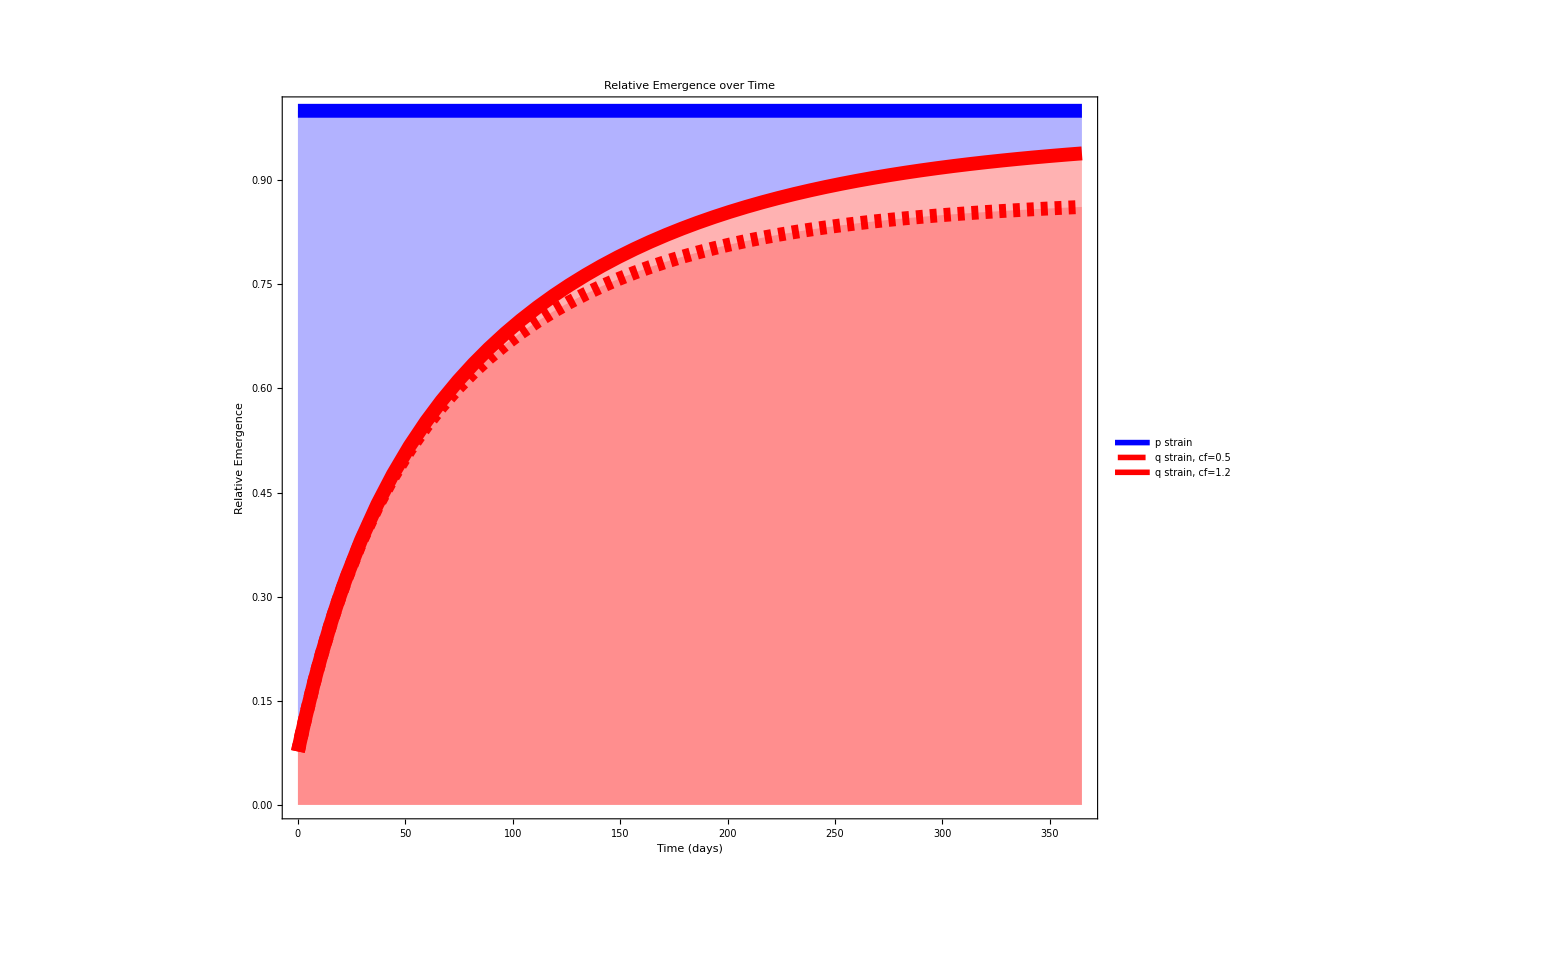

```mathematica
Plot[Evaluate[
{1,
NDSolveValue[Evaluate[Join[EQN[0.5,False],IC[0.5,False,False]]],(Iall[q][t])/(Iall[p][t]+Iall[q][t]),{t,0,365}],
NDSolveValue[Evaluate[Join[EQN[2,False],IC[0.5,False,False]]],(Iall[q][t])/(Iall[p][t]+Iall[q][t]),{t,0,365}]}
],
{t,0,365},
PlotLegends->(Style[#,50]&/@{"p strain","q strain, cf=0.5","q strain, cf=1.2"}),
PlotStyle->{Directive[AbsoluteThickness[10],Blue],Directive[AbsoluteThickness[10],Red,Dashed],Directive[AbsoluteThickness[10],Red]},
Filling->{1->{{3},Directive[Blue,Opacity[0.3]]},2->{Axis,Directive[Red,Opacity[0.2]]},3->{Axis,Directive[Red,Opacity[0.3]]}},
PlotRange->{0,1},ImageSize->1600,FrameTicksStyle->Directive[45],
PlotLabel->Style["Relative Emergence over Time",110],
Axes->False,Frame->{True,True,False,False},FrameLabel->Evaluate[Style[#,85]&/@{"Time (days)","Relative Emergence"}]
]
Export[NotebookDirectory[]<>"Figure 1.png",%];
```

```mathematica
Manipulate[
Plot[Evaluate[
NDSolveValue[Evaluate[Join[EQN[cf,False],IC[pp,False,False]]],{Iall[q][t]+Iall[p][t],Iall[q][t]},{t,0,tmax}]
],
{t,0,tmax},
PlotLegends->{"p strain","q strain"},
PlotStyle->{Blue,Red},
Filling->{1->{{2},Directive[Blue,Opacity[0.3]]},2->{Axis,Directive[Red,Opacity[0.3]]}},
PlotRange->{0,15000}
],
{{cf,1},0.5,2},{{pp,0},0,1},
{{tmax,365},30,2*365}
]
```

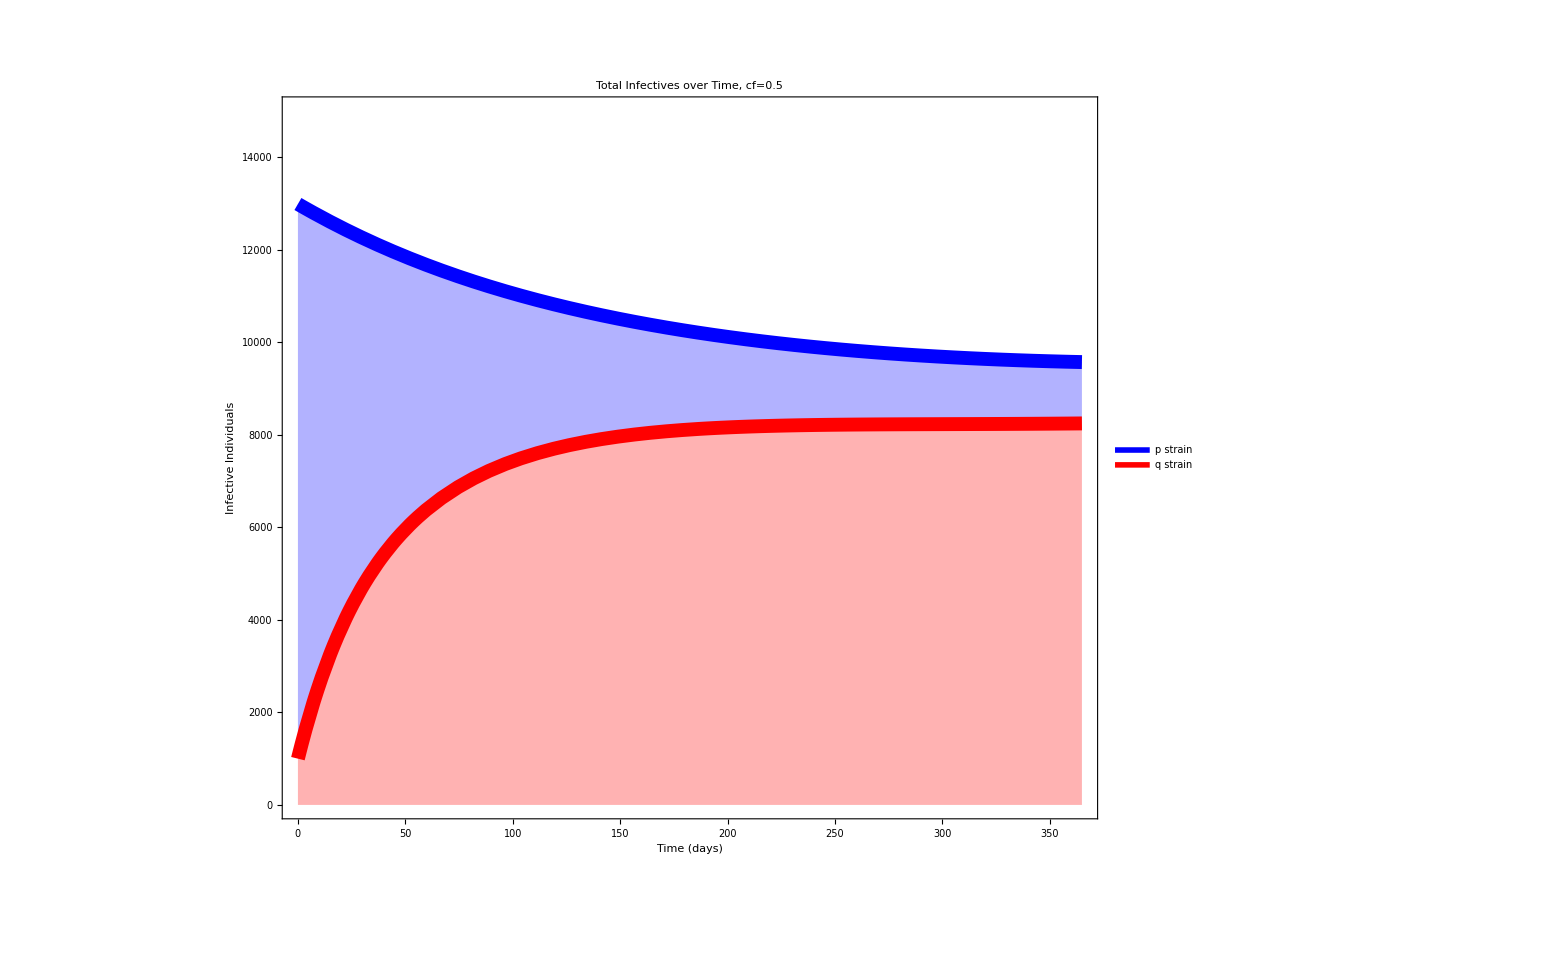

```mathematica
Plot[Evaluate[
NDSolveValue[Evaluate[Join[EQN[0.5,False],IC[0.5,False,False]]],{Iall[q][t]+Iall[p][t],Iall[q][t]},{t,0,365}]
],
{t,0,365},
PlotLegends->(Style[#,50]&/@{"p strain","q strain"}),
PlotStyle->{Directive[AbsoluteThickness[10],Blue],Directive[AbsoluteThickness[10],Red]},
FrameTicksStyle->Directive[45],
Filling->{1->{{2},Directive[Blue,Opacity[0.3]]},2->{Axis,Directive[Red,Opacity[0.3]]}},
PlotRange->{0,15000},ImageSize->1600,
PlotLabel->Style["Total Infectives over Time, cf=0.5",100],
Axes->False,Frame->{True,True,False,False},FrameLabel->Evaluate[Style[#,85]&/@{"Time (days)","Infective Individuals"}]
]
Export[NotebookDirectory[]<>"Figure 2a.png",%];
```

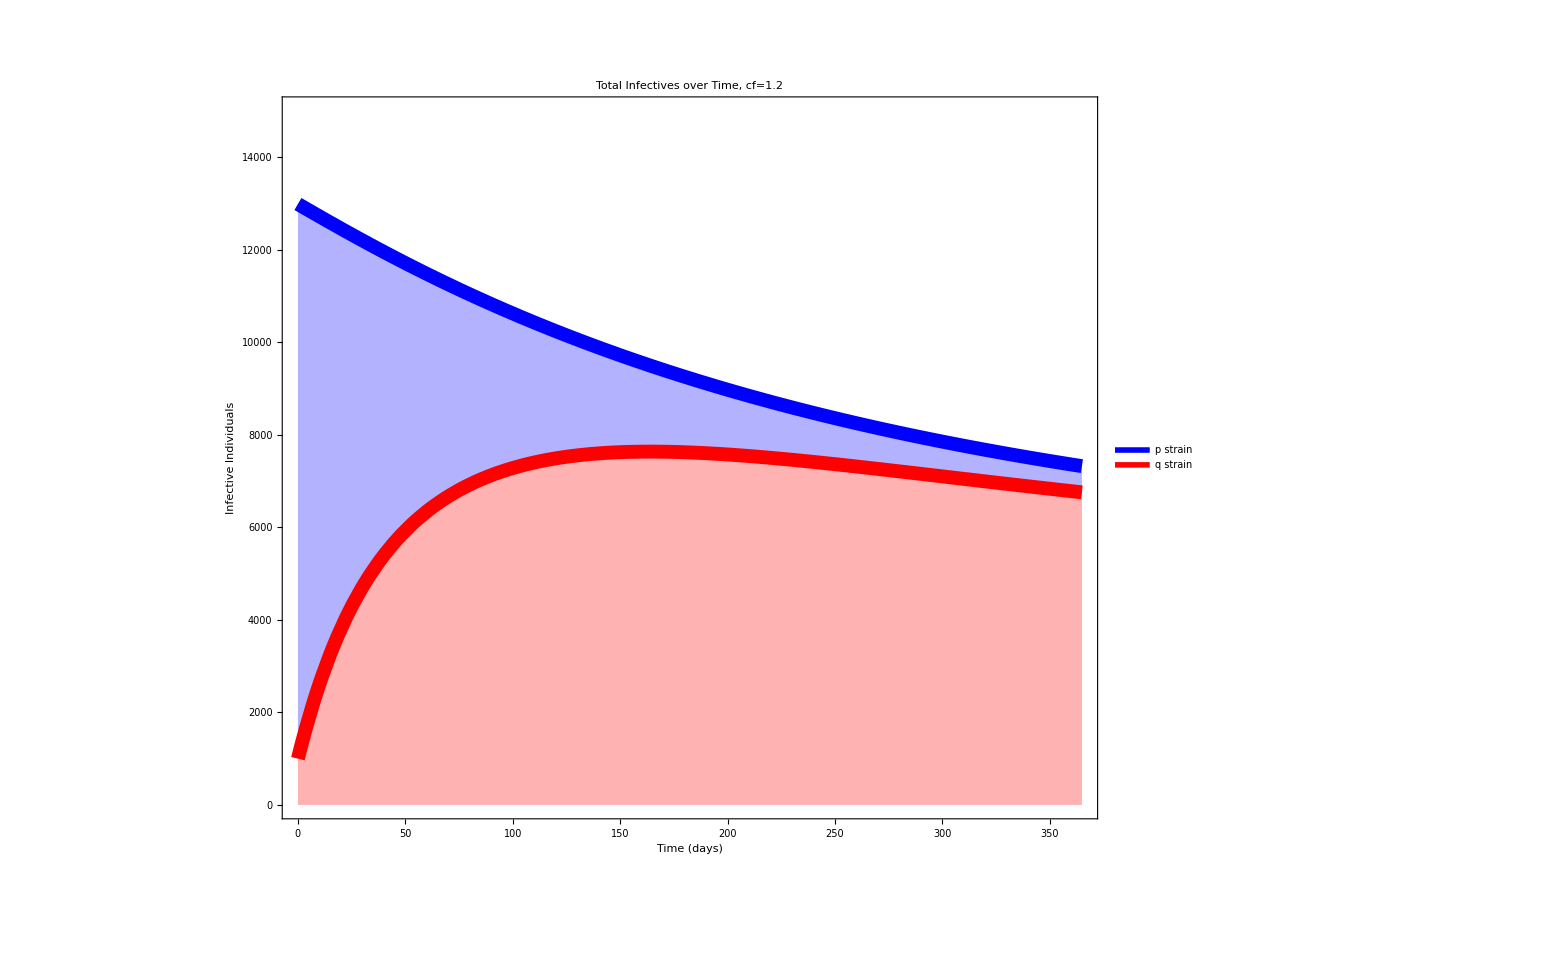

```mathematica
Plot[Evaluate[
NDSolveValue[Evaluate[Join[EQN[1.2,False],IC[1.2,False,False]]],{Iall[q][t]+Iall[p][t],Iall[q][t]},{t,0,365}]
],
{t,0,365},
PlotLegends->(Style[#,50]&/@{"p strain","q strain"}),
PlotStyle->{Directive[AbsoluteThickness[10],Blue],Directive[AbsoluteThickness[10],Red]},FrameTicksStyle->Directive[45],
Filling->{1->{{2},Directive[Blue,Opacity[0.3]]},2->{Axis,Directive[Red,Opacity[0.3]]}},
PlotRange->{0,15000},ImageSize->1600,
PlotLabel->Style["Total Infectives over Time, cf=1.2",100],
Axes->False,Frame->{True,True,False,False},FrameLabel->Evaluate[Style[#,85]&/@{"Time (days)","Infective Individuals"}]
]
Export[NotebookDirectory[]<>"Figure 2b.png",%];
```

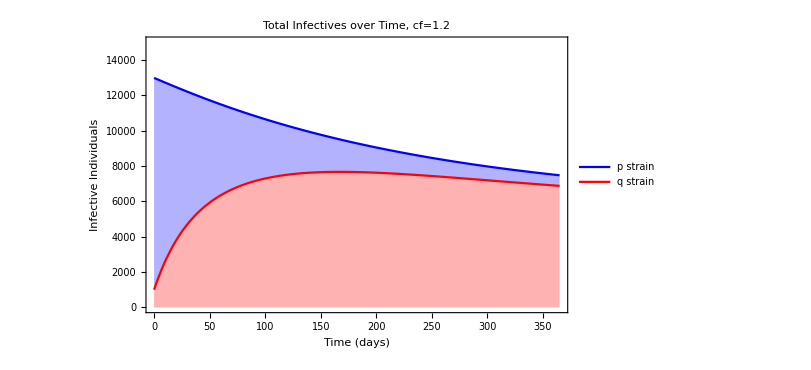

```mathematica
Plot[Evaluate[
NDSolveValue[Evaluate[Join[EQN[1.2,False],IC[0.5,False,False]]],{Iall[q][t]+Iall[p][t],Iall[q][t]},{t,0,365}]
],
{t,0,365},
PlotLegends->{"p strain","q strain"},
PlotStyle->{Blue,Red},
Filling->{1->{{2},Directive[Blue,Opacity[0.3]]},2->{Axis,Directive[Red,Opacity[0.3]]}},
PlotRange->{0,15000},ImageSize->600,
PlotLabel->"Total Infectives over Time, cf=1.2",
Axes->False,Frame->{True,True,False,False},FrameLabel->{"Time (days)","Infective Individuals"}
]
(*Export[NotebookDirectory[]<>"CH3-infectives-cf1.2.png",%]*)
```

```mathematica
SOL[cf_,pp_,noq_:False,noaids_:False,tmax_:365]:=
NDSolveValue[Evaluate[Join[Evaluate[EQN[cf,noq]],Evaluate[IC[pp,noq,noaids]]]],{Iall[p][t],Iall[q][t]},Evaluate[{t,0,tmax}]]
```

```mathematica
NUMB[cf_,pp_,noq_:False,noaids_:False,tmax_:365]:=Integrate[Evaluate[SOL[cf,pp,noq,noaids,tmax]],{t,1,tmax}]
```

```mathematica
data=Flatten[Table[{cf,pp,NUMB[cf,pp]},{cf,0.5,1.2,0.1},{pp,0,1,0.1}],1];
```

```mathematica
(*data=Flatten[Table[{cf,pp,NUMB[cf,pp]},{cf,0.5,1.2,0.05},{pp,0,1,0.05}],1];
Export[NotebookDirectory[]<>"dataBEST.csv",data];*)1
data=ToExpression[Import[NotebookDirectory[]<>"dataBEST.csv"]];
```

1

```mathematica
data1={#[[1]],#[[2]],#[[3,2]]}&/@data;
data2={#[[1]],#[[2]],(#[[3,2]])/(#[[3,1]]+#[[3,2]])}&/@data;
```

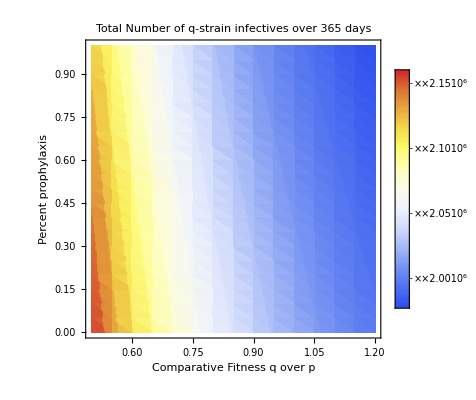

```mathematica
ListDensityPlot[data1,ColorFunction->"TemperatureMap",PlotLegends->Automatic,
FrameLabel->{"Comparative Fitness q over p","Percent prophylaxis"},
PlotLabel->"Total Number of q-strain infectives over 365 days",
MeshFunctions->{#3&},Mesh->10]
```

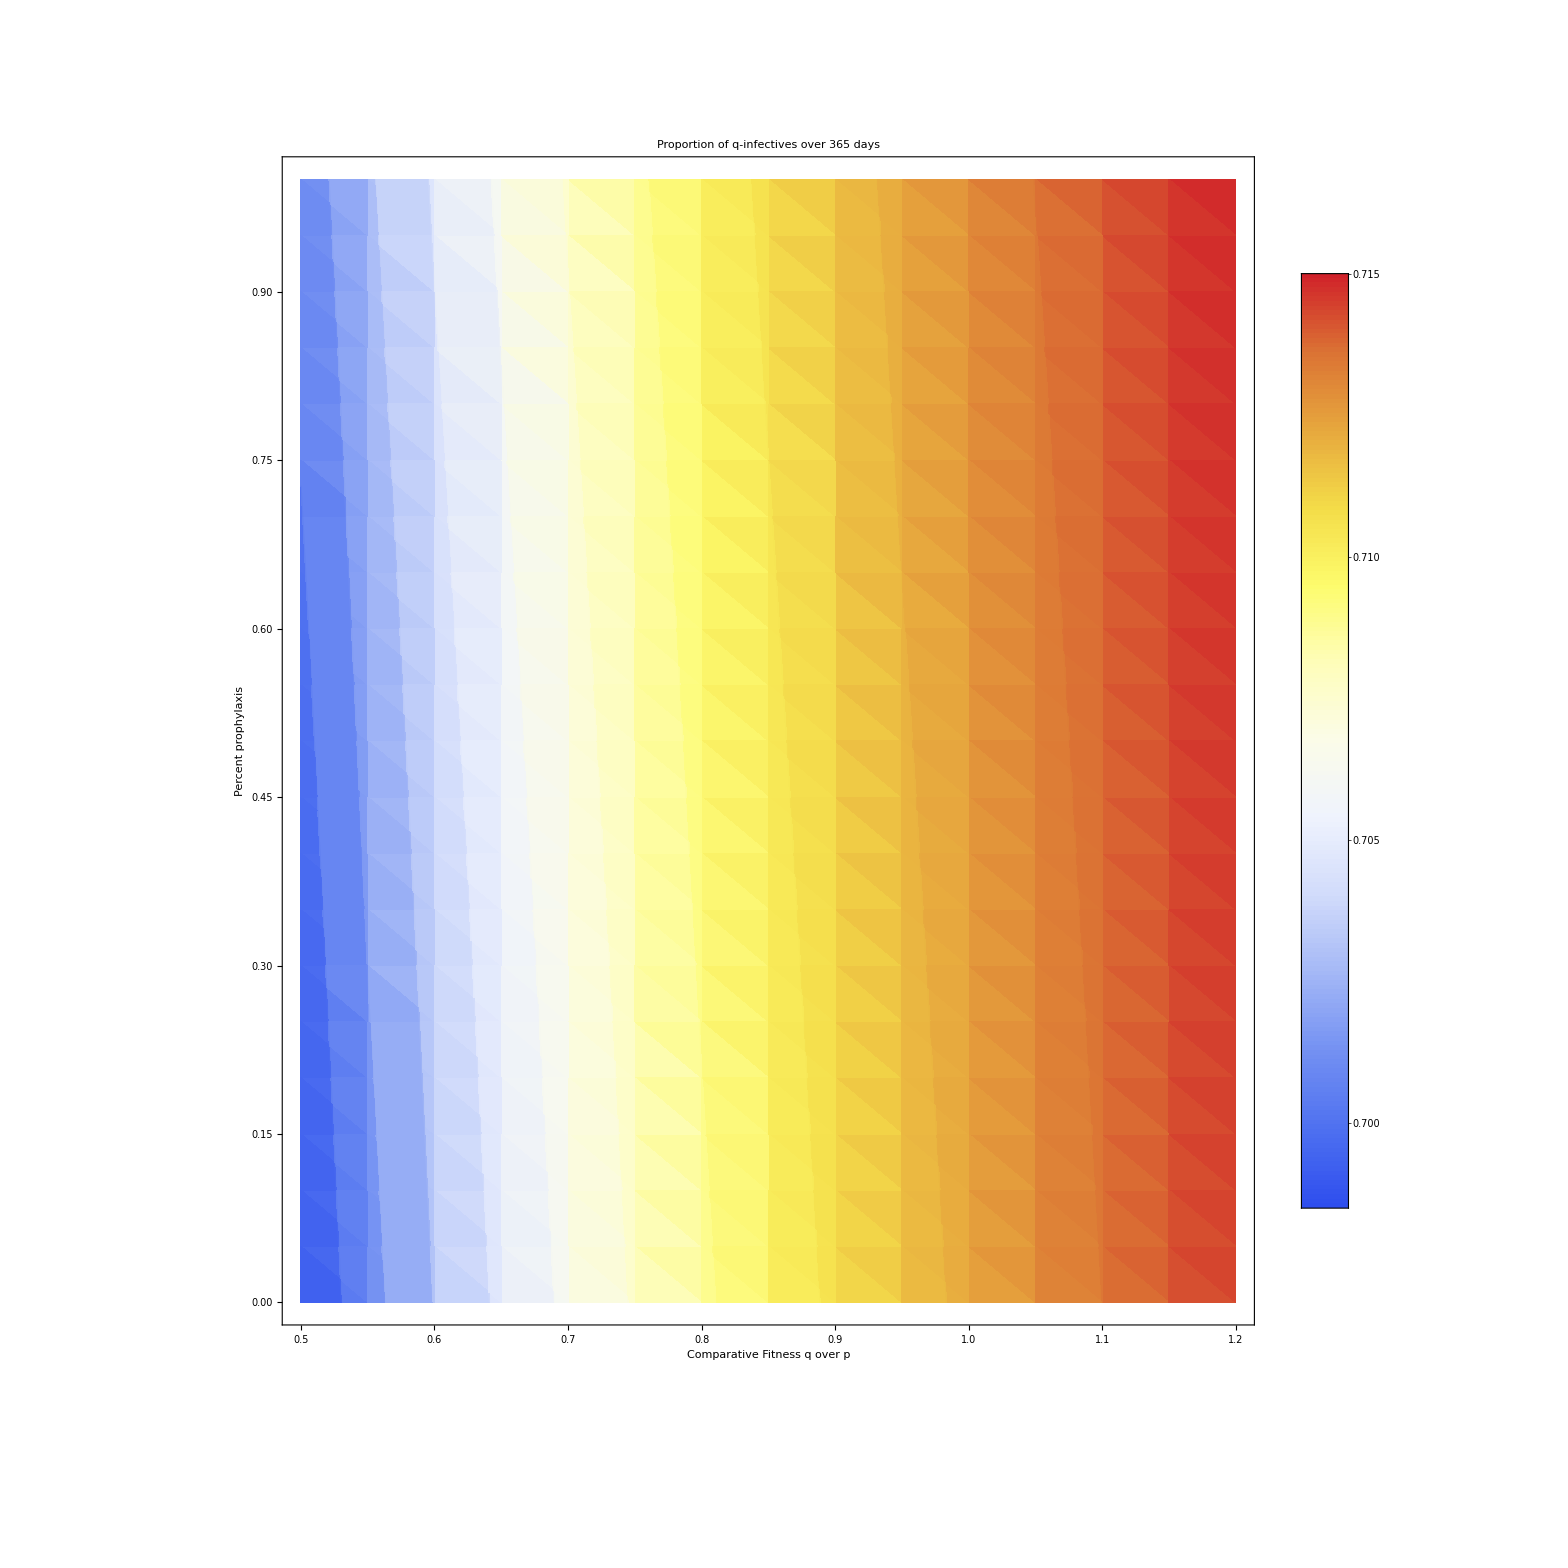

E:\feffercode\AD ch3 - Impact of Strain Competition\Figure 4.png

```mathematica
ListDensityPlot[data2,ColorFunction->"TemperatureMap",
PlotLegends->BarLegend[{"TemperatureMap",MinMax[data2[[All,3]]]},LabelStyle->Directive[45],LegendMarkerSize->{100,800}],
FrameLabel->Evaluate[Style[#,75]&/@{"Comparative Fitness q over p","Percent prophylaxis"}],
PlotLabel->Style["Proportion of q-infectives over 365 days\n",85],
FrameTicksStyle->Directive[45],
ImageSize->1600,MeshFunctions->{#3&},Mesh->10]
Export[NotebookDirectory[]<>"Figure 4.png",%]
```